```mathematica
ClearAll["Global`*"]
```

```mathematica
Adata={76,82,96,100,116,128,130,150};
DeltaN={1.376,2.225,1.436,2.129,1.952,1.798,1.791,0.981};
(* daugther *)
SQRTA={1.491,1.435,1.326,1.3,1.207,1.149,1.140,1.061};
(* 1/3sqrtA*)
```

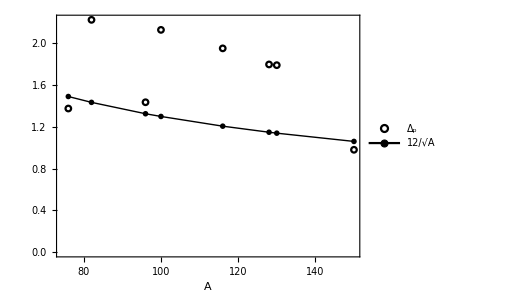

```mathematica
plot=ListPlot[{Table[{Adata[[i]],DeltaN[[i]]},{i,1,Length[Adata]}],Table[{Adata[[i]],SQRTA[[i]]},{i,1,Length[Adata]}]},Joined->{False, True},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],LabelStyle->{22,Bold,Black,FontFamily->"Times"},FrameLabel->{"A"},PlotRange->All,PlotStyle->{{Black},{Black,Thick}},PlotMarkers->{{Graphics[{Circle[]}],1/18},{Graphics[{Disk[]}],1/20}},PlotLegends->Placed[{"Δ_p","12/√A"},{0.8,0.18}],ImageSize->380];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/Delta-plots/figure-4/figure-4.pdf",Show[plot],ImageResolution->1200];
Show[plot]
```